```mathematica
(* Cross Product Visual *)
a = {1, 0, 0};
b = 1/2{1, √3, 0};
origin = {0, 0, 0};

crossDiagram =Graphics3D[{
(*Opacity[.5], (* Makes area of Parallelogram transparent *)
Yellow,
Polygon[{origin, a, a+b,  b}], (* Forms Parallelogram made by a and b*)
Opacity[1], *)
GrayLevel[0],  
Arrow[{origin, a}], (* Vector a *)
Text[Style[Pane["a", ImageMargins-> 1], 20, Bold], (1/2)a-{0, .1, 0}],
Arrow[{origin, b}], (* Vector b *)
Text[Style[Pane["b", ImageMargins-> 1], 20, Bold], (1/2)b-{.2, 0, 0}],
Arrow[{origin, Cross[a, b]}], (* Vector a × b *)
Text[Style[Pane["a × b", ImageMargins-> 1], 20, Bold], (1/2)Cross[a, b] + {0, .2, 0}]
}]; 
Show[crossDiagram, Boxed -> False]
```

-Graphics3D-

```mathematica
(* Parallelepiped Visual *)
a = {1, 0, 0};
b = 1/2{1, √3, 0};
c = 1/2{1, 1, √3};
origin = {0, 0, 0};
h=Graphics[Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]];

parallelepiped =Graphics3D[{
GrayLevel[0.3,0.2],
Parallelepiped[origin, {a, b, c}], (* Forms Parallelogram made by a and b*)
Opacity[1],
GrayLevel[0], 
Arrow[{origin, a}], (* vector a *)
Text[Style[Pane["a", ImageMargins-> 1], 20, Bold], (1/2)a-{0, .1, 0}], 
Arrow[{origin, b}], (* Vector b *)
Text[Style[Pane["b", ImageMargins-> 1], 20, Bold], (1/2)b-{.2, 0, 0}],
Arrow[{origin, c}], (* Vector a × b *)
Text[Style[Pane["c", ImageMargins-> 1], 20, Bold], (1/2)Cross[a, b] + {0, .2, 0}],
Text[Style[Pane["a⋀b⋀c", ImageMargins->1], 20, Bold], (a + b + c)/2],
Arrowheads[{{Automatic, Automatic, h}}],
Arrow[{a+b, (a + {{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}.b)}],
Arrow[{a, (b/2 + {{1, 0, 0}, {0, 0, 0}, {0, 0, 0}}.a)}]
}]; 
Show[parallelepiped, Boxed -> False]
```

-Graphics3D-

```mathematica
(* Bivector Visual *)
scale = 2;
a = scale{1, 0, 0};
b =(scale / 2){1, √3, 0};
h=Graphics[Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]];
origin = {0, 0, 0};

bivector =Graphics3D[{
GrayLevel[0.3,0.2],
Polygon[{origin, a, a+b,  b}], (* Forms Parallelogram made by a and b*)
Opacity[1],
GrayLevel[0],  
Arrow[{origin, a}], (* Vector a *)
Text[Style[Pane["a", ImageMargins-> 1], 20, Bold], (1/2)a-{0, scale/10, 0}],
Arrow[{origin, b}], (* Vector b *)
Text[Style[Pane["b", ImageMargins-> 1], 20, Bold], (1/2)b-{(2 scale)/10, 0, 0}],
Text[Style[Pane["a ⋀ b", ImageMargins-> 1], 20, Bold], (a + b)/2],
Arrowheads[{{Automatic,Automatic,h}}],
Arrow[{a+b, (a + {{0, 0, 0}, {0, 1, 0}, {0, 0, 0}}.b)}],
Arrow[{a, (b/2 + {{1, 0, 0}, {0, 0, 0}, {0, 0, 0}}.a)}]
}]; 
Show[bivector, Boxed -> False]
```

-Graphics3D-

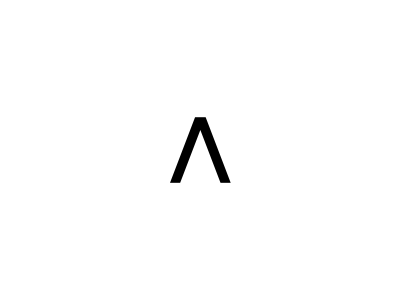

```mathematica
Graphics[Text[Style[Pane["⋀"], 300, Bold]]]
```